## Лабораторная работа №7

Координаты точек первоначального многоугольника : {{2,7},{15,2},{24,12},{11,21},{5,15},{2,7}}

Координаты рандомной точки = {{20,23}}

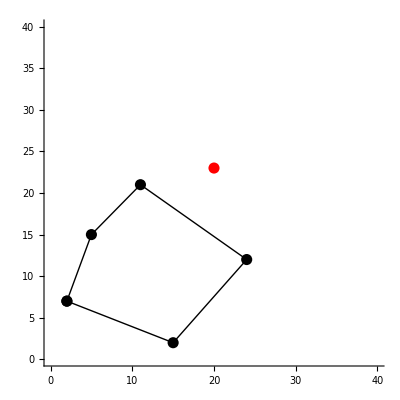

Массив точек выпуклой оболочки : {{11,21},{5,15},{2,7},{2,7},{15,2},{24,12},{20,23}}

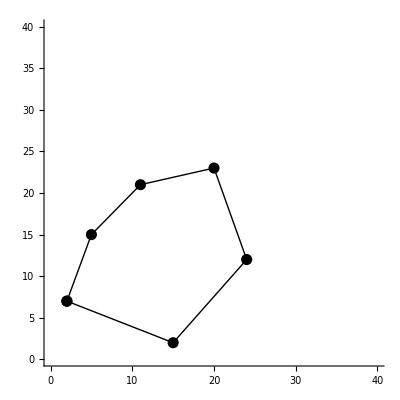

```mathematica
(*Задаем многоугольник*)
P={{2,7},{15,2},{24,12},{11,21},{5,15}};
AppendTo[P,P[[1]]];
Print["Координаты точек первоначального многоугольника : ",P];
PointLocation[p1_,p2_,p3_]:=Det[{p2-p1,p3-p1}];

S={};(*рандомная точка*)
L={};
(*задаем рандомную точку*)
AppendTo[S,{RandomInteger[35],RandomInteger[35]}];
Print["Координаты рандомной точки = ",S];

(*Изображаем график, отображающий многоугольник и рандомную точку*)
Graphics[{PointSize[.02],
Point/@P,Red, Point /@S, Black,
Line[Append[P,P⟦1⟧]]},
PlotRange-> {{0, 40}, {0,40}}, Axes->True,
AspectRatio -> Automatic]

(*добавляем счетчик*)
k=0;
For[j=1,j≤Length[P]-1,j++,(*пробегаемся циклом по всем точкам многоугольника*)
If[PointLocation[P[[j]],P[[j+1]],S[[1]]]≥0,k++](*если рандомная точка располагается слева от стороны многоугольника или на стороне, то прибавляем к счетчику единицу*)
];
If[k==5,AppendTo[L,S[[1]]]]; (*если значение счетчика равно количеству точек многоугольника, то запоминаем координаты рандомной точки в L*)
If[Length[L]== 0,(*если значение L все же осталось пустым (т.е.рандомная точка располагается за пределами многоугольника*)
R={};
For[j=1,j≤Length[P]-1,j++,(*пробегаемся циклом по всем точкам многоугольника*)
If[PointLocation[P[[j]],P[[j+1]],S[[1]]]<0,AppendTo[R,P[[j]]];AppendTo[R,P[[j+1]]]] (*если рандомная точка располагается справа от стороны многоугольника, то добавляем в массив R координаты точек, задающих сторону многоугольника*)];
(*в следующей части кода мы по факту удаляем лишнюю точку из R в случае, если рандомная точка попадет на уровень угла многоугольника (т.е. в таком случае получится, что данная точка располагается справа относительно сразу двух сторон и получится, что одна из точек будет добавлена дважды*)
n=Length[R];
For[k=1,k≤n-1,k++,
For[j=2,j≤n,j++,
If[k≠j,
If[(R[[k,1]]==R[[j,1]])&&(R[[k,2]]==R[[j,2]]),R=Drop[R,{k}];n--]]
];
];

(*создаем пустой массив для координат выпуклой оболочки*)
Z={};
start=0;(*задаем переменную для точки от которой мы будем вести прямую к рандомной точке для построения выпуклой оболочки*)
end=0;(*задаем переменную для точки к которой мы будем вести прямую от рандомной точки для замыкания выпуклой оболочки*)
(*по сути start и end - это вершины многоугольника, между которыми располагается рандомная точка*)
For[j=1,j≤Length[P],j++,
If[(P[[j,1]]==R[[n,1]])&&(P[[j,2]]==R[[n,2]]),end=j,(*присваиваем переменной end индекс вершины многоугольника, координаты которой совпадают с координатами последнего элемента массива R*)
If[(P[[j,1]]==R[[1,1]])&&(P[[j,2]]==R[[1,2]]),start=j](*присваиваем переменной start индекс вершины многоугольника, координаты которой совпадают с координатами первого элемента массива R*)
]
];


If[start≠Length[P],(*если "стартовая" точка не является последней вершиной многоугольника*)
For[r=end,r≤Length[P],r++,(*добавляем в массив выпуклой оболочки координаты вершин от end до последней вершины самого многоугольника*)
AppendTo[Z,P[[r]]]
];
For[r=1,r≤start,r++,(*а также добавляем в массив выпуклой оболочки координаты вершин от первой вершины самого многоугольника до start*)
AppendTo[Z,P[[r]]]
];
AppendTo[Z,S[[1]]], (*в конце добавляем в массив выпуклой оболочки координату рандомной точки*)
For[r=end,r≤start,r++,(*если все же стартовая точка равна последней вершине многоугольника (т.е. рандомная точка располагается между последней вершиной и первой, то добаляем в массив выпуклой оболочки все вершины по порядку начиная с первой до последней, а в конец массива выпуклой оболочки добавляем координаты рандомной вершины*)
AppendTo[Z,P[[r]]]
];AppendTo[Z,S[[1]]]
];

Print["Массив точек выпуклой оболочки : ",Z];
S=Drop[S,{1}],



Print["Точка оказалась внутри многоугольника, значит строить выпуклую оболочку заново смысла нет"];S=Drop[S,{1}]];

(*если длина массива L равна нулю (т.е. это значит, что точка лежит снаружи многоугольника), то изображаем график выпуклой оболочки*)
If[Length[L]==0,Graphics[{PointSize[.02],
Point/@Z,  Black,
Line[Append[Z,Z[[1]]]]},
PlotRange-> {{0, 40}, {0,40}}, Axes->True,
AspectRatio -> Automatic]]
```